# Laura Bialozynski - Capstone Lesson

## Collaborators: Fiona Gleeson & Katie Utz

In this lesson, we’re going to use the Mathematica skills we’ve developed over the quarter to explore and understand a collection of combinatorial objects called derangements. It will be convenient to make the notation [n] = {1, 2,…, n}.

Definition 1.  A derangement of [n] is a permutation σ = σ_1 σ_2(…σ)_n of [n] with no fixed points. (This kind of notation for a permutation is called one-line notation.) A fixed point of a permutation σ is an index i such that σ_i= i. For example, in the permutation {3, 1, 2} of [3], we have σ_1=3,σ_2= 2, σ_3=1 , and so 2 is a fixed point.

In Mathematica, permutations are stored as a list. (We’ve already seen Permutations as a tool for generating them.) Let d_n denote the number of derangements of [n], with d_0=1 by convention. Here are a few other values of d_n. Make sure you can see why the values are what they are. d_1=0, d_2= 1, d_3=2.

The following exercises represent a guided exploration of how Mathematica (and computation in general) can be used as a tool for mathematical research.

#### Exercise 1

1. Write a function NumFixedPoints[p_List] that takes a permutation p as input and returns the number of fixed points of p.

```mathematica
NumFixedPoints[p_List]:=Count[Table[p[[i]]==i,{i,Range[Length[p]]}],True]
```

```mathematica
NumFixedPoints[{1,2,3,5,4,6}]
```

4

2. Using your function from part 1, write a function GetPermutationsByFixedPoints[n_Integer, k_Integer] that takes integers n, k as inputs and returns the list of permutations of [n] having exactly k fixed points.

```mathematica
GetPermutationsByFixedPoints[n_Integer,k_Integer]:=Select[Permutations[Range[n]],NumFixedPoints[#]==k&]
```

```mathematica
GetPermutationsByFixedPoints[4,2]
```

{{1,2,4,3},{1,3,2,4},{1,4,3,2},{2,1,3,4},{3,2,1,4},{4,2,3,1}}

3. Using your function from part 2, write a function GetDerangements[n_Integer] that takes an integer n as an input and returns the list of derangements of [n].

```mathematica
GetDerangements[n_Integer]:=GetPermutationsByFixedPoints[n,0]
```

```mathematica
GetDerangements[4]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

4. Write a function GetNonDerangements[n_Integer] that takes an integer n as an input and returns the list of permutations of [n] which are not derangements.

```mathematica
GetNonDerangements[n_Integer]:=Complement[Permutations[Range[n]],GetDerangements[n]]
```

```mathematica
GetNonDerangements[4]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,3,1,4},{2,4,3,1},{3,1,2,4},{3,2,1,4},{3,2,4,1},{4,1,3,2},{4,2,1,3},{4,2,3,1}}

#### Exercise 2

1. Find all the derangements of [4]. How many are there?

```mathematica
GetDerangements[4]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

```mathematica
Length[GetDerangements[4]]
```

9

```mathematica
(*We can see that there are 9 derangements of {1, 2, 3, 4}.*)
```

2. Using Map or Table, create a list of length 9 whose i-th element is the number of derangements of [i]. Enter this sequence into the OEIS and find the sequence number corresponding to d_n.

```mathematica
Map[Length[GetDerangements[#]]&,Range[9]]
```

{0,1,2,9,44,265,1854,14833,133496}

```mathematica
(*According to OEIS this sequence of numbers is defined by a(n)equals(n-1)*(a(n-1)+a(n-2)) and a(n) equals n*a(n-1)+(-1)^n or the number of permutations of n elements with no fixed points A000166.*)
```

3. Use RandomChoice to produce a random derangement of [9].

```mathematica
RandomChoice[GetDerangements[9]]
```

{3,7,5,6,9,8,4,1,2}

4. Find the average number of fixed points among 100 randomly chosen permutations of [9]. (Hint: Your answer here should be close to 1. This will be explored further in Exercise 9.)

```mathematica
Mean[RandomChoice[NumFixedPoints[#]&/@Permutations[Range[9]],100]]
```

93/100

#### Exercise 3

1. Write a function LargestFixedPoint[p_List] that takes a permutation p (which is not a derangement) and returns the value of the largest fixed point of p.

```mathematica
LargestFixedPoint[p_List]:=Module[{n={},i=1},While[i≤Length[p],If[p[[i]]==i,AppendTo[n,p[[i]]]];i++];Max[n]]
```

```mathematica
LargestFixedPoint[{1,2,3,4}]
```

4

2. Write a function ComputeSum[n_Integer] that takes an integer n and returns the sum of the values of the largest fixed point over all permutations of [n] which are not derangements. Use the function from part 4 of Exercise 1.

```mathematica
Clear[ComputeSum]
```

```mathematica
ComputeSum[n_Integer]:=Plus@@Map[LargestFixedPoint,GetNonDerangements[n]]
```

```mathematica
ComputeSum[4]
```

44

3. Map your function from part 2 across Range[8]. You should notice something amazing. Provide a conjecture about these numbers.

```mathematica
ComputeSum/@Range[8]
```

{1,2,9,44,265,1854,14833,133496}

```mathematica
(*We observe that these are the same numbers that we saw before. This leads us to believe that the sum of the largest fixed points of all permutations of a series of numbers 1 through n gives us the number of derangements there are for that specific number n.*)
```

#### Exercise 4

1. Using Array, write a function PermutationMatrix[p_List] that takes a permutation p as input and returns a matrix whose (i,j) entry is 1 if p_i= j and is 0 otherwise. This matrix is called a permutation matrix corresponding to the permutation p.

```mathematica
PermutationMatrix[p_List]:=Array[If[p[[#1]]==#2,1,0]&,{Length[p],Length[p]}]
```

```mathematica
PermutationMatrix[{1,4,3,2,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)

2. Mathematica can produce random permutations using RandomPermutation. Mathematica returns the permutation in cycle notation - this can be converted into one-line notation using the function PermutationList. Produce a random permutation p of length 20 and use ArrayPlot to visualize the permutation matrix corresponding to p.

```mathematica
PermutationList[RandomPermutation[20]]
```

{20,18,6,2,11,19,5,13,3,9,7,16,14,17,12,1,4,10,15,8}

```mathematica
ArrayPlot[PermutationMatrix[PermutationList[RandomPermutation[20]]]]
```

-Graphics-

3. Map the function ArrayPlot across the list of permutation matrices corresponding to all of the derangements of [5]. What do you notice about the diagrams and how does this tie in with their definition?

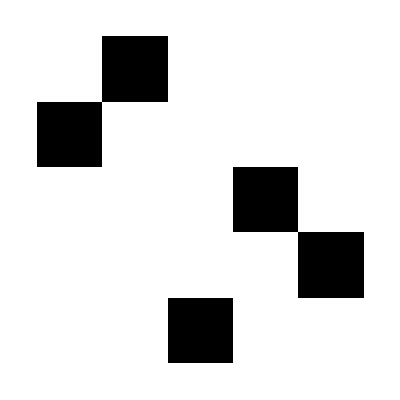
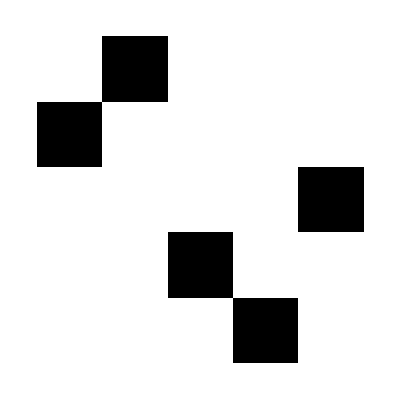
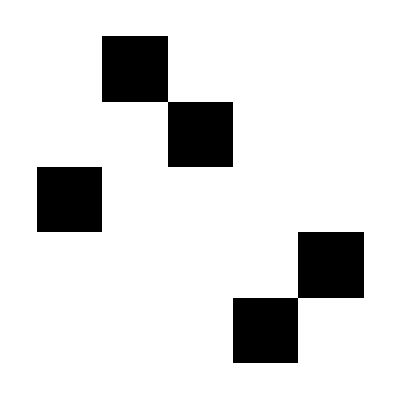
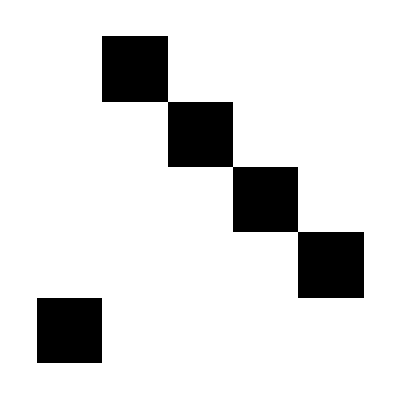
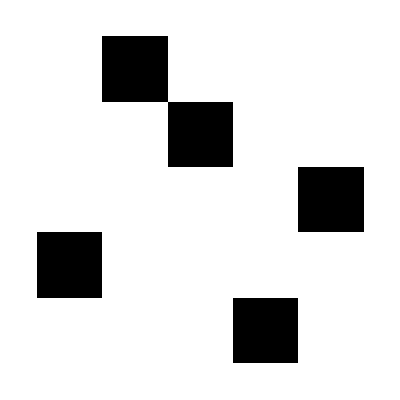
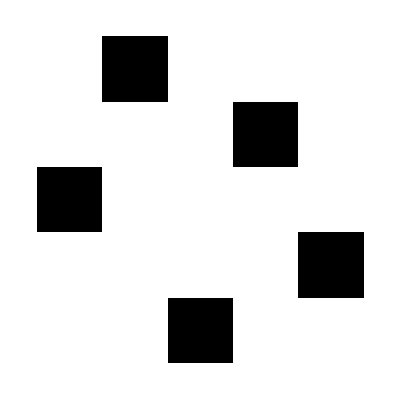
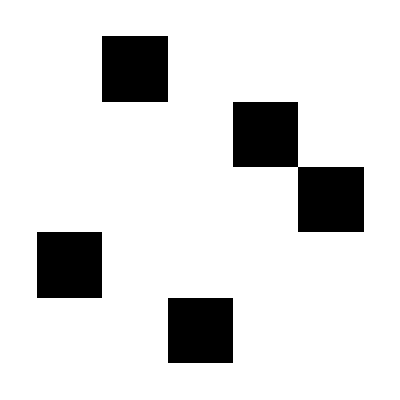
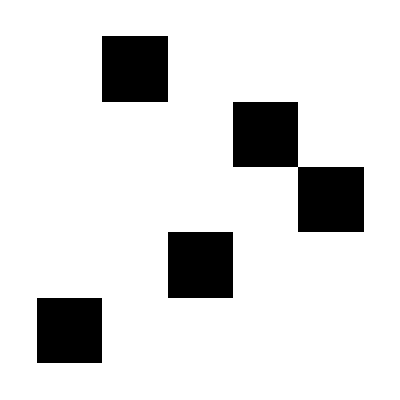

```mathematica
ArrayPlot/@(PermutationMatrix[#]&/@GetDerangements[5])
```

```mathematica
(*We notice that none of the diagrams have a black square along the diagonal (where we would have 1's in an identity matrix). This makes sense because we are only looking at derangements, which are where no number is in its original location. We would expect for none of our derangements in ArrayPlot to have any black squares along the diagonal because this would mean that we have a value in its original location which is contradictory to the definition of a derangement.*)
```

#### Exercise 5

1. Write a function called GetSum[n_Integer] which computes the sum

∑_(i=0)^n (-1)^i(n!)/(i!)

and map this function across Range[9].

```mathematica
GetSum[n_Integer]:=Sum[(((-1)^i(n!))/(i!)),{i,0,n}]
```

```mathematica
Map[GetSum[#]&,Range[9]]
```

{0,1,2,9,44,265,1854,14833,133496}

2. Let f_n be the sequence defined by f_0=1 and f_n = n f_(n-1)+(-1)^n. Write a recursive program (using memoization) which computes f_n. Map this function across Range[9].

```mathematica
f[0]=1;
```

```mathematica
f[n_]:=f[n]=n*f[n-1] + (-1)^n
```

```mathematica
Map[f[#]&,Range[9]]
```

{0,1,2,9,44,265,1854,14833,133496}

3. What do you conjecture about the values of the outputs of GetSum and the function that you wrote in (b)? In particular, how do they compare to the sequence d_n? It should be obvious what is being asked here, and although we have only provided a small amount of evidence, it turns out to be true for all n.

```mathematica
(*The calues of the outputs of GetSum and the function written in part (b) above look to be the same as the sequence Subscript[d, n]. We know that when we only have one number in a sequence there can be no derangements because there is only one permutation and when there are two numbers in a sequence there is only one derangement of the two possible permutations. It is also obvious to see by listing out by hand that when we have 3 elements there are only 2 possible derangements of the six (3!) total permutations and similarly when there are 4 elements we have 9 possible derangements of the twenty-four (4!) total permutations. This starts to become difficult to manage when we involve more unique elements as going up to just 5 elements means that we have 5! or 120 possible permutations and we can see from our output above that only 44 of these are derangements. It is most important to note that both the values of the outputs of GetSum and the function written in part (b) appear to be the same as the sequencec Subscript[d, n] as far as we can tell for these values.*)
```

#### Exercise 6

This exercise investigates the probability that a random permutation of [n] is a derangement.

1. Use ListPlot and either one of the functions from Exercise 5 to plot the probability that a random permutation of [n] is a derangement for 1 <= n <= 20. Set the PlotRange to be from 0 to 1/2.

```mathematica
?ListPlot
```

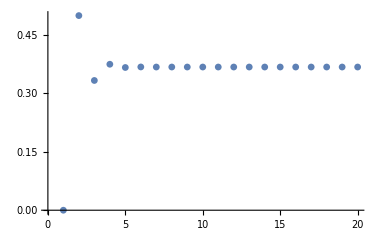

```mathematica
ListPlot[Map[f[#]/(#!)&,Range[20]],PlotRange->{0,1/2}]
```

2. Do you suspect that this probability converges as n -> ∞? If yes, provide an estimate of this value.

```mathematica
(*Yes based on the plot above it appears that this probability converges as n approaches infinity. It looks like as n approaches infinity our probability stabilizes around 0.36 or 0.37 so we would estimate that the probability converges to a value of somewhere between 0.36 and 0.37.*)
```

3. Add a dashed, green horizontal line y = 1/ⅇ to your plot from (a). What do you notice?

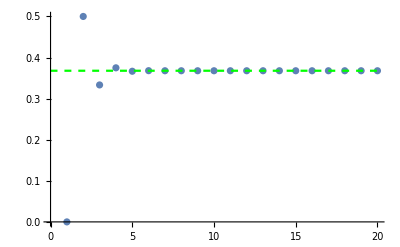

```mathematica
Show[ListPlot[Map[f[#]/(#!)&,Range[20]],PlotRange->{0,1/2}],{Plot[(1/E),{x,0,20},PlotStyle->{Green, Dashed}]}]
```

```mathematica
1/E//N
```

0.367879

```mathematica
(*From plotting the horizontal line y equal 1/e above we notice that it appears as if the probability points that we plotted above converge to this value. In the beginning the probabilities seem very unstable and in no specific pattern but they quickly stabilize along this line. We can see from a simple computation above that 1/e is approximately equal to 0.367879 and we estimated that our probability values converged to a point between 0.36 and 0.37. This gives us evidence that the probability converges to 1/e as n approaches infinity.*)
```

#### Exercise 7

1. It turns out that d_n = (n-1) (d_(n-1) + d_(n-2)). Generate some data to convince yourself of this fact.

```mathematica
d[0]=0;
```

```mathematica
d[1]=0;
```

```mathematica
d[2]=1;
```

```mathematica
d[n_]:=d[n]=(n-1)(d[n-1]+d[n-2])
```

```mathematica
Map[d[#]&,Range[9]]
```

{0,1,2,9,44,265,1854,14833,133496}

```mathematica
(*We can see that this formula gives us the same output as we saw in the previous exercise above and we know from computing by hand for small values that at least the first few elements of this list are correct for the number of derangements of a permutation of a certain size. This also makes sense based on the properties that are required for a specific permutation to be classified as a derangement.*)
```

2. Consider (without Mathematica) the function F defined by the infinite power series formula

F(t) = ∑_(n>=0)^∞ d_n/(n!)t^n

(This is called the exponential generating function for the sequence {d_n}_(n >= 0).) It is possible to use recursion from 1 to show that F(t) satisfies the differential equation

(1 - t) F'(t) = t F(t), F(0) = 1.

Use Mathematica to solve this equation for F(t).

```mathematica
Clear[F]
```

```mathematica
DSolveValue[{(1-t)*(F'[t])==t*F[t],F[0]==1}, F[t],t]
```

-ⅇ^-t/(-1+t)

3. Verify that n! times the coefficient of t^n is indeed equal to d_n for 1 <= n <= 9. The function SeriesCoefficient will come in handy.

```mathematica
Table[(v!)*SeriesCoefficient[Series[Sum[(d[n]/n!)*t^n,{n,0,9}],{t,0,9}],v]==d[v],{v,1,9}]
```

{True,True,True,True,True,True,True,True,True}

4. Use Plot to graph the solution found in part 2 for -3 <= t <= 3. Use ParametricPlot (or ContourPlot) and Show to include a red, dashed vertical line at the asymptote on the plot.

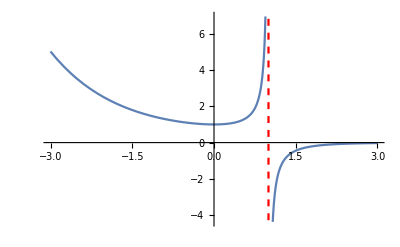

```mathematica
Show[Plot[-(E^-t)/(t-1),{t,-3,3}],ParametricPlot[{1,y},{y,-100,100},PlotStyle->{Dashed, Red}]]
```

#### Exercise 8

Let e_(0,0)=1, e_(0,k)=0 for all k >0. Otherwise, let e_(n,k) denote the number of permutations of [n] having exactly k fixed points.

1. Write a program that computes e_(n,k). Make use of the function your wrote in part 2 of Exercise 1.

```mathematica
ComputeE[0,0]=1;
```

```mathematica
ComputeE[0,k_]:=0;
```

```mathematica
ComputeE[n_Integer,k_Integer]:=Length[GetPermutationsByFixedPoints[n,k]]
```

```mathematica
ComputeE[4,3]
```

0

2. Using Array, create a 9 × 9 matrix A whose (n,k) entry is e_(n-1,k-1).

```mathematica
Array[ComputeE[#1-1,#2-1]&,{9,9}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
9 | 8 | 6 | 0 | 1 | 0 | 0 | 0 | 0
44 | 45 | 20 | 10 | 0 | 1 | 0 | 0 | 0
265 | 264 | 135 | 40 | 15 | 0 | 1 | 0 | 0
1854 | 1855 | 924 | 315 | 70 | 21 | 0 | 1 | 0
14833 | 14832 | 7420 | 2464 | 630 | 112 | 28 | 0 | 1)

```mathematica
|
```

3. Using a single line of code, verify that the n-th row sum of A is equal to (n-1)! for all 1 <= n <= 9. (A row sum is just the total of the entries in the row.)

```mathematica
A=Array[ComputeE[#1-1,#2-1]&,{9,9}]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{2,3,0,1,0,0,0,0,0},{9,8,6,0,1,0,0,0,0},{44,45,20,10,0,1,0,0,0},{265,264,135,40,15,0,1,0,0},{1854,1855,924,315,70,21,0,1,0},{14833,14832,7420,2464,630,112,28,0,1}}

```mathematica
(*The line of code above is just defining our matrix to make use of it quicker and easier in the following problems.*)
```

```mathematica
Table[Total[A[[j]]]==(j-1)!,{j,1,9,1}]
```

{True,True,True,True,True,True,True,True,True}

```mathematica
(*This is our single line of code that verifies that the above statement holds true for our matrix.*)
```

4. Is A invertible? Is A diagonalizable?

```mathematica
Inverse[A]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{-1,0,1,0,0,0,0,0,0},{-2,-3,0,1,0,0,0,0,0},{-3,-8,-6,0,1,0,0,0,0},{-4,-15,-20,-10,0,1,0,0,0},{-5,-24,-45,-40,-15,0,1,0,0},{-6,-35,-84,-105,-70,-21,0,1,0},{-7,-48,-140,-224,-210,-112,-28,0,1}}

```mathematica
%//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-2 | -3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-3 | -8 | -6 | 0 | 1 | 0 | 0 | 0 | 0
-4 | -15 | -20 | -10 | 0 | 1 | 0 | 0 | 0
-5 | -24 | -45 | -40 | -15 | 0 | 1 | 0 | 0
-6 | -35 | -84 | -105 | -70 | -21 | 0 | 1 | 0
-7 | -48 | -140 | -224 | -210 | -112 | -28 | 0 | 1)

```mathematica
A.Inverse[A]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(*This shows us that our matrix A is invertible because we were able to find the inverse of our matrix and when we multiply our original matrix by its own inverse we get the identity matrix as expected.*)
```

1. Write a function Diagonalize[A_] that returns the pair of matrices {P, D} such that D = P^-1 A P if A is diagonalizable and returns 0 otherwise.

```mathematica
matrixD[A_]:=Array[Which[#1==#2,Subscript[a, #1#2]=Eigenvalues[A][[#1]],
						#1≠#2,Subscript[a, #1#2]=0]&,{Length[A],Length[A]}]
```

```mathematica
Diagonalize[A_]:=Which[
Det[Eigenvectors[A]]==0,0,
A==Eigenvectors[A].matrixD[A].Inverse[Eigenvectors[A]],{Eigenvectors[A],matrixD[A]},
A!=Eigenvectors[A].matrixD[A].Inverse[Eigenvectors[A]],0]
```

```mathematica
Diagonalize[A]
```

0

```mathematica
(*Using code from a previous homework assignment on determining whether a matrix is diagonalizable we apply this code to our matrix A and the output tells us that this matrix is not diagonalizable because the output of 0 means that we can not diagonalize this matrix.*)
```

5. Looking at the first two columns of A, conjecture for which n it is more likely that a random permutation of [n] has 0 fixed points than a single fixed point.

```mathematica
(*We can see that matrix A's first row corresponds to n = 0 and its second row corresponds with n = 1 and so on. We can further note that for the first, third, and all subsequent odd rows the first column value is bigger than the second column value which shows that for all even values of n from 0 to 8 there are more permutations of n with no fixed points than 1 fixed point. The conjecture we can make from this is that when n is even it is more likely that a random permutation of [n] will have 0 fixed points than it is that the random permutation of [n] will have 1 fixed point.*)
```

#### Exercise 9

Using the definition of e_(n,k) from Exercise 8, consider (without Mathematica) the function defined by the infinite power series in two variables given by

F(t,x) = ∑_(n>=0) ∑_(k>=0) (e_(n,k))/(n!)x^k t^n.

Fact:  F(t, x) = e^(t(x-1))/(1-t).

1. Suppose that n is a fixed positive integer. Let X_n be the random variable determined by the outcome of the following experiment: select a permutation of [n] uniformly at random (i.e. each permutation is equally likely) and count the number of fixed points.

a. The expectation of this random variable, denoted E(X_n), is

E(X_n) = 1/(n!)∑_(k >= 0) k e_(n,k).

It  can be shown that E(X_n) is exactly the coefficient of t^n in

∂/(∂x)F(t, x)|_(x = 1).

Use this fact and Mathematica to produce {E(X_1), E(X_2), …, E(X_20)} (the list of expectations of X_1 through X_20). 		Provide a conjecture for the value of E(X_n) for any positive integer n.

```mathematica
F[t_,x_]:=E^(t(x-1))/(1-t)
```

```mathematica
D[F[t,x],x]/.x->1
```

t/(1-t)

```mathematica
Series[t/(1-t),{t,0,20}]
```

t+t^2+t^3+t^4+t^5+t^6+t^7+t^8+t^9+t^10+t^11+t^12+t^13+t^14+t^15+t^16+t^17+t^18+t^19+t^20+O[t]^21

```mathematica
Table[SeriesCoefficient[Series[t/(1-t),{t,0,20}],i],{i,1,20}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Conjecture: E(Subscript[X, n]) = 1 for all positive integers n.*)
```

b. The variance of this random variable, denoted V(X_n), is defined by

E(X_n^2) - E(X_n)^2.

It can shown that E(X_n^2) is precisely the coefficient of t^n in

∂/(∂x)(x ∂/(∂x)F(t, x))_(x = 1).

Use this fact and Mathematica to produce {V(X_1), V(X_2), …, V(X_20)} (the list of variances).  Provide a conjecture for the value of V(X_n) for any positive integer n.

```mathematica
D[x D[F[t,x],x],x]/.x->1
```

t/(1-t)+t^2/(1-t)

```mathematica
Series[t/(1-t) + t^2/(1-t),{t,0,20}]
```

t+2 t^2+2 t^3+2 t^4+2 t^5+2 t^6+2 t^7+2 t^8+2 t^9+2 t^10+2 t^11+2 t^12+2 t^13+2 t^14+2 t^15+2 t^16+2 t^17+2 t^18+2 t^19+2 t^20+O[t]^21

```mathematica
Table[SeriesCoefficient[Series[t/(1-t) + t^2/(1-t),{t,0,20}],i],{i,1,20}]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Table[SeriesCoefficient[Series[t/(1-t) + t^2/(1-t),{t,0,20}],i],{i,1,20}]-Table[SeriesCoefficient[Series[t/(1-t),{t,0,20}],i],{i,1,20}]
```

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Conjecture: V(Subscript[X, n]) = 0 for n=1 and V(Subscript[X, n]) = 1 for all positive integers greater than 1.*)
```

2. Using Array, create a 9 × 9 matrix B whose (n, k) entry is equal to (n-1)! times the coefficient of x^(k-1)t^(n-1) in F(t, x). Provide evidence for the Fact above by showing that the matrix B is equal to the matrix A from Exercise 8. Again, SeriesCoefficient will come in handy, even when working with a power series in multiple variables.

```mathematica
B=Array[(#1-1)!SeriesCoefficient[F[t,x],{t,0,#1-1},{x,0,#2-1}]&,{9,9}]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{2,3,0,1,0,0,0,0,0},{9,8,6,0,1,0,0,0,0},{44,45,20,10,0,1,0,0,0},{265,264,135,40,15,0,1,0,0},{1854,1855,924,315,70,21,0,1,0},{14833,14832,7420,2464,630,112,28,0,1}}

```mathematica
B//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
9 | 8 | 6 | 0 | 1 | 0 | 0 | 0 | 0
44 | 45 | 20 | 10 | 0 | 1 | 0 | 0 | 0
265 | 264 | 135 | 40 | 15 | 0 | 1 | 0 | 0
1854 | 1855 | 924 | 315 | 70 | 21 | 0 | 1 | 0
14833 | 14832 | 7420 | 2464 | 630 | 112 | 28 | 0 | 1)

```mathematica
(*The matrix B that we see above is the same as matrix A from Exercise 8.*)
```

3. Use Plot3D to graph the function F(t,x) for -3 <= t, x <= 3; set the PlotRange to 3, PlotPoints to 35, and the AspectRatio to 1. You’ll notice that Mathematica includes some gray clipping where the function is “cut off”. Use ClippingStyle to remove the clipping, ColorFunction to make the surface have a “Rainbow” coloring. Then use ParametricPlot3D (or ContourPlot3D) to include a 30% opaque (see Opacity) vertical plane with no meshlines (see Mesh) at the asymptote on the plot.

```mathematica
Show[Plot3D[F[t,x],{t,-3,3},{x,-3,3},PlotRange->3,PlotPoints->35,AspectRatio->1,ClippingStyle->None,ColorFunction->"Rainbow"],ParametricPlot3D[{1,x,z},{x,-3,3},{z,-3,3},PlotStyle->Opacity[.3],Mesh->None]]
```

-Graphics3D-